```mathematica
KnownPoints={};
```

```mathematica
UpPoint[pnt_]:={Exp[pnt],1+Values[pnt]};
DownPoint[pnt_]:={Log[pnt],Values[pnt]-1};

AddPoint[pnt_,val_]:=(
If[MemberQ[KnownPoints,pnt],
Print["The point " ,pnt," is already known with value " ,Values[pnt] , " and new value is " , val]];

AppendTo[KnownPoints,pnt];
Values[pnt]=val;
);

AddPointChain[pnt_,val_,depth_]:=Module[{cpnt,cval},
AddPoint[pnt,val];
cpnt=pnt;
For[i=0,i<depth,i++,
{cpnt,cval}=UpPoint[cpnt];
AddPoint[cpnt,cval];
];
cpnt=pnt;
For[i=0,i<depth,i++,
{cpnt,cval}=DownPoint[cpnt];
AddPoint[cpnt,cval];
];
];

PlotKnownPoints[rmin_,rmax_]:=Module[{rpoints, rvals, ppoints},
rpoints=Cases[KnownPoints,p_/;Im[p]==0&&rmin≤p≤rmax];
rvals=Values/@rpoints;
ppoints=Transpose[{rpoints,rvals}];
(*Print[Sort[ppoints]];*)
ListPlot[ppoints,DataRange->{rmin,rmax}]
];
```

The point Indeterminate is already known with value -1. and new value is -2.

The point Indeterminate is already known with value -2. and new value is -3.

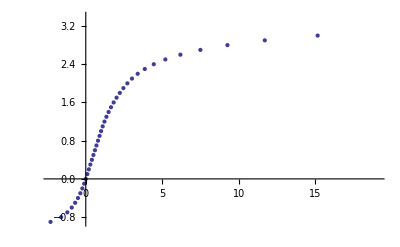

```mathematica
m=0.0;
KnownPoints={};
For[p=m,p<Exp[m],p+=0.1,
AddPointChain[p,p,3]];
PlotKnownPoints[-100,100]
```

```mathematica
m=0;
KnownPoints={};
For[p=m,p<Exp[m],p+=0.1,
r=(p-m)/(Exp[m]-m);
v=(1-r)*m+r*(1+m);
AddPointChain[p,v,3]];
PlotKnownPoints[-100,100]
```

The point ∞ is already known with value -2 and new value is -3

-Graphics-

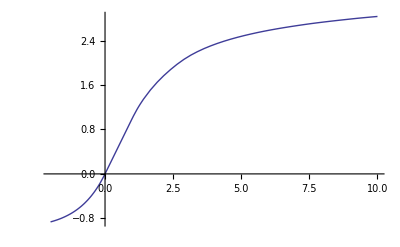

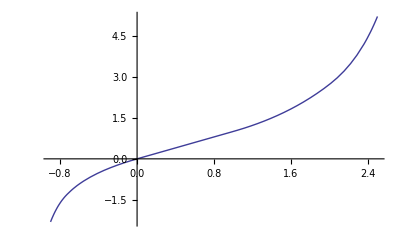

```mathematica
ConstructRealInterpolator:=Module[{rpoints, rvals, ppoints,ipoints},
rpoints=Cases[KnownPoints,p_/;Im[p]==0&&-Infinity<p<Infinity];
rvals=Values/@rpoints;
ppoints=Transpose[{rpoints,rvals}];
ipoints=Transpose[{rvals,rpoints}];
{Interpolation[ppoints],Interpolation[ipoints]}
];

{phi,iphi}=ConstructRealInterpolator;
Plot[phi[x],{x,-2,10}]
Plot[iphi[x],{x,-0.9,2.5}]
```

```mathematica
gexp[x_,p_]:=iphi[p+phi[x]];
SqrtExp[x_]=gexp[x,0.5];
```

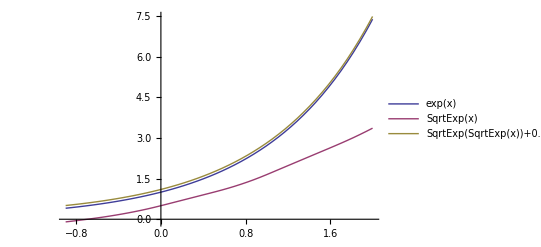

```mathematica
Plot[{Exp[x],SqrtExp[x],SqrtExp[SqrtExp[x]]+0.1},{x,-0.9,2},PlotLegends->"Expressions"]
```

```mathematica
Manipulate[Plot[{Exp[Exp[x]], Exp[x],gexp[x,p],x,Log[x]},{x,-0.9,10},PlotLegends->"Expressions",PlotRange->{-3,8}],{{p,0.5},-0.3,2}]
```

```mathematica
Manipulate[Plot[{Exp[x],gexp[x,p],x,Log[x]},{x,-2,3},PlotLegends->"Expressions",PlotRange->{-5,5}],{{p,0},-1,1}]
```

InterpolatingFunction::dmval: Input value {-1.25378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.35878} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.50378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.29378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.65378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.20878} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.76878} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.14378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.943781} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.43578} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.64378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.85378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.86378} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.42378} lies outside the range of data in the interpolating function. Extrapolation will be used.

## Complex interpolation

```mathematica
ComplexInterpolation[pnts_]:=Module[{rpnts,ipfunc},
rpnts=pnts/.{pnt_?NumberQ,val_}->{{Re[pnt],Im[pnt]},val};
ipfunc=Interpolation[rpnts,InterpolationOrder->1];
ipfunc[Re[#],Im[#]]&
];
```

```mathematica
ComplexInterpolation[{{1+2I,3},{4+5I,6},{7,9}}]
```

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

ipfunc$540820[Re[#1],Im[#1]]&

```mathematica
PlotComplex[f_,rng_]:=Module[{rmin,imin,rmax,imax},
{rmin,imin,rmax,imax}=rng/.{Complex[rmin_,imin_],Complex[rmax_,imax_]}->{rmin,imin,rmax,imax};
GraphicsRow[{
DensityPlot[Abs[f[x+y I]],{x,rmin,rmax},{y,imin,imax},PlotLabel->"Abs",ColorFunction->"TemperatureMap"],
DensityPlot[Arg[f[x+y I]],{x,rmin,rmax},{y,imin,imax},PlotLabel->"Arg",ColorFunction->"TemperatureMap"]
}]
];

PlotComplexReIm[f_,rng_]:=Module[{rmin,imin,rmax,imax},
{rmin,imin,rmax,imax}=rng/.{Complex[rmin_,imin_],Complex[rmax_,imax_]}->{rmin,imin,rmax,imax};
GraphicsRow[{
DensityPlot[Re[f[x+y I]],{x,rmin,rmax},{y,imin,imax},PlotLabel->"Re",ColorFunction->"TemperatureMap"],
DensityPlot[Im[f[x+y I]],{x,rmin,rmax},{y,imin,imax},PlotLabel->"Im",ColorFunction->"TemperatureMap"]
}]
];
```

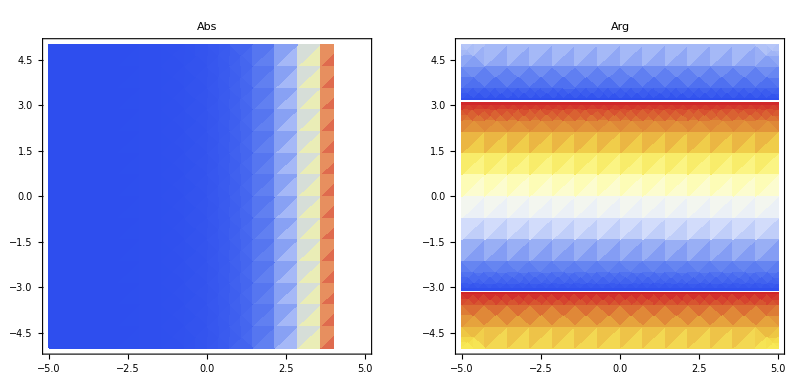

```mathematica
PlotComplex[Exp,{-5-5I,5+5I}]
```

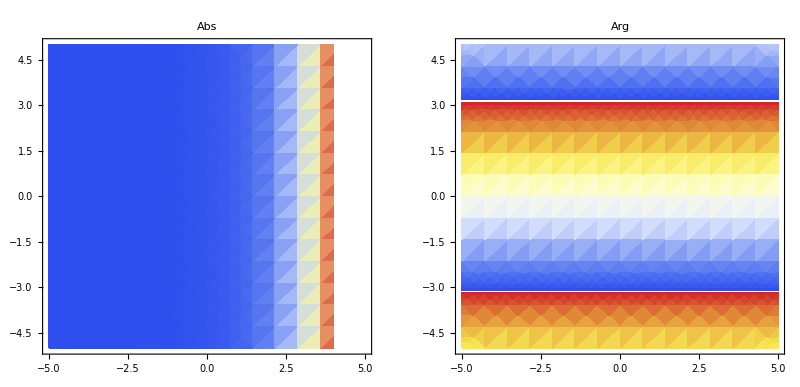

```mathematica
idata=Flatten[Table[{x+y I,Exp[x+y I]},{x,-5,5,0.2},{y,-5,5,0.2}],1];
iexp=ComplexInterpolation[idata];
PlotComplex[iexp,{-5-5I,5+5I}]
```

```mathematica
PlotComplexKnownPoints[rmin_,rmax_]:=Module[{rpoints, cpoints},
rpoints=Cases[KnownPoints,p_/;rmin≤Abs[p]≤rmax];
cpoints=rpoints/.Complex[a_,b_]->{a,b};
ListPlot[cpoints,DataRange->{rmin,rmax}]
];
```

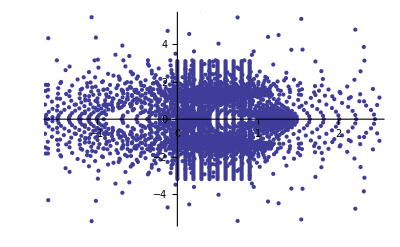

```mathematica
m=0.0;
KnownPoints={};
For[p=m,p<Exp[m],p+=0.1,
For[ip=-3.2,ip<3.2,ip+=0.1,
AddPointChain[p+I*ip,p+I*ip,3]]];
PlotComplexKnownPoints[-10,10]
```

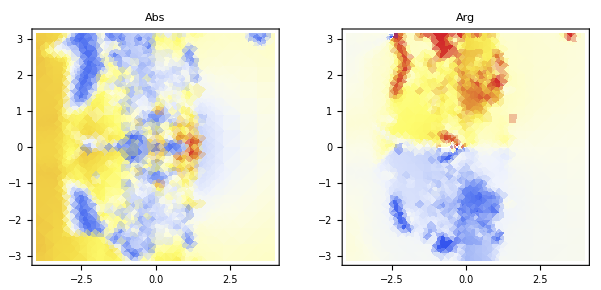

InterpolatingFunction::dmval: Input value {-3.99943, -3.13955} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3.42857, -2.69143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

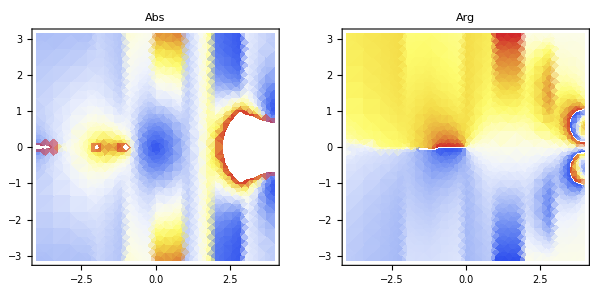

```mathematica
ConstructComplexInterpolator:=Module[{rpoints, rvals, ppoints,ipoints},
rpoints=Cases[KnownPoints,p_/;-Infinity<Abs[p]<Infinity];
rvals=Values/@rpoints;
ppoints=Transpose[{rpoints,rvals}];
ipoints=Transpose[{rvals,rpoints}];
{ComplexInterpolation[ppoints],ComplexInterpolation[ipoints]}
];

{phi,iphi}=ConstructComplexInterpolator;
PlotComplex[phi,{-4-3.14 I,4+3.14 I}]
PlotComplex[iphi,{-4-3.14 I,4+3.14 I}]
```

```mathematica
gexp[x_,p_]:=iphi[p+phi[x]];
SqrtExp[x_]=gexp[x,0.5];
```

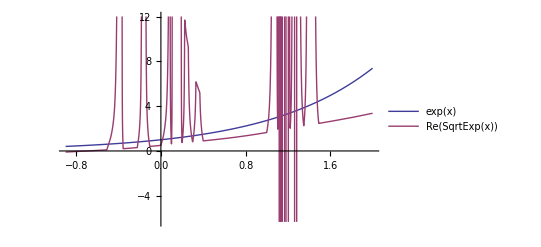

```mathematica
Plot[{Exp[x],Re[SqrtExp[x]]},{x,-0.9,2},PlotLegends->"Expressions"]
```

```mathematica
phi[1.5]
```

1.40521-1.09268×10^-17 ⅈ

```mathematica
IterExp[val_,depth_]:=
Which[
depth==0,val,
depth<0,IterExp[Log[val],depth+1],
depth>0,If[Re[val]<100,IterExp[Exp[val],depth-1],Overflow[]]
];
FindIterDepths[val_]:=Module[{ies,depths,maxdepth=5},
ies=Table[{depth,IterExp[val,depth]},{depth,-maxdepth,maxdepth}];
depths=Cases[ies,{depth_,valu_}:>{-depth,valu}/;0≤ Re[valu]<1];
depths=Sort[depths,Abs[#1[[1]]]<Abs[#2[[1]]]&];
depths
];
FindMinIterDepth[val_]:=FindIterDepths[val][[1,1]];
```

```mathematica
FindIterDepths[-1+2I]//N
```

{{1.,0.804719+2.03444 ⅈ},{-2.,0.81049+0.281705 ⅈ},{2.,0.782903+1.19413 ⅈ},{3.,0.356204+0.990478 ⅈ},{4.,0.0512453+1.22557 ⅈ},{5.,0.204279+1.52901 ⅈ}}

```mathematica
FindMinIterDepth[-15]
```

-1

```mathematica
DensityPlot[FindMinIterDepth[a+b I],{a,-3,3},{b,-5,5},
ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

-Graphics-

```mathematica
RepFunc[f_,reps_]:=If[reps==0,#&,f[RepFunc[f,reps-1][#]]&];
```

```mathematica
logpnts=N[Table[RepFunc[Log,n][2+3I],{n,0,50}]];
logpnts//MatrixForm
```

(2.+3. ⅈ
1.28247+0.982794 ⅈ
0.479795+0.653868 ⅈ
-0.209468+0.937758 ⅈ
-0.0399188+1.79056 ⅈ
0.582777+1.59309 ⅈ
0.52847+1.2201 ⅈ
0.284904+1.16205 ⅈ
0.179376+1.33037 ⅈ
0.294462+1.43677 ⅈ
0.382972+1.36865 ⅈ
0.351516+1.29796 ⅈ
0.296181+1.30632 ⅈ
0.292277+1.34784 ⅈ
0.321476+1.35725 ⅈ
0.332755+1.33822 ⅈ
0.32134+1.32708 ⅈ
0.311473+1.33323 ⅈ
0.314175+1.34129 ⅈ
0.320338+1.34071 ⅈ
0.320959+1.33626 ⅈ
0.317921+1.33507 ⅈ
0.316562+1.33702 ⅈ
0.317715+1.33831 ⅈ
0.318822+1.33771 ⅈ
0.318584+1.33683 ⅈ
0.317919+1.33685 ⅈ
0.31782+1.33732 ⅈ
0.318139+1.33747 ⅈ
0.318299+1.33727 ⅈ
0.318184+1.33712 ⅈ
0.31806+1.33718 ⅈ
0.31808+1.33728 ⅈ
0.318152+1.33728 ⅈ
0.318166+1.33723 ⅈ
0.318132+1.33721 ⅈ
0.318114+1.33723 ⅈ
0.318125+1.33725 ⅈ
0.318139+1.33724 ⅈ
0.318137+1.33723 ⅈ
0.31813+1.33723 ⅈ
0.318128+1.33724 ⅈ
0.318131+1.33724 ⅈ
0.318133+1.33724 ⅈ
0.318132+1.33723 ⅈ
0.318131+1.33723 ⅈ
0.318131+1.33724 ⅈ
0.318132+1.33724 ⅈ
0.318132+1.33724 ⅈ
0.318132+1.33724 ⅈ
0.318131+1.33724 ⅈ)

```mathematica
ToPlane[cpnts_]:=cpnts/.(c_/;NumberQ[c]):>{Re[c],Im[c]};
```

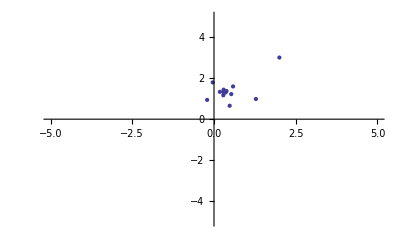

```mathematica
ListPlot[ToPlane[logpnts],PlotRange->{{-5,5},{-5,5}}]
```

```mathematica
Abs[0.3181313071392835+1.3372356194010797 ⅈ]
```

1.37456

```mathematica
Exp[.3181313]
```

1.37456

```mathematica
ExpFixPoint=RepFunc[Log,200][1.1]
```

0.318132+1.33724 ⅈ

```mathematica
ComplexCircleAround[c_,r_,n_]:=(c+r Exp[#I]&)/@Array[#&,n,{0,2π}];
```

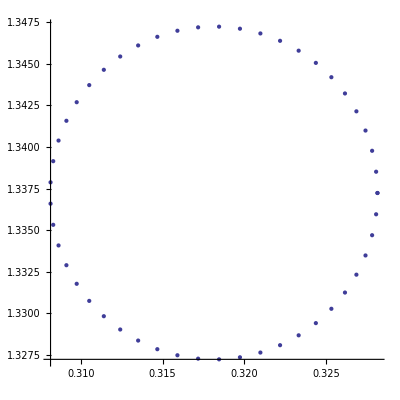

```mathematica
ListPlot[ToPlane[ComplexCircleAround[ExpFixPoint,0.01,50]],AspectRatio->1]
```

```mathematica
Manipulate[ListPlot[ToPlane[RepFunc[Exp,reps]/@ComplexCircleAround[ExpFixPoint,0.1,50]],AspectRatio->1,PlotRange->{{-2,2},{-2,2}}],{reps,0,20,1}]
```

```mathematica
Manipulate[ListPlot[ToPlane[RepFunc[Log,reps]/@ComplexCircleAround[ExpFixPoint,0.1,50]],AspectRatio->1,PlotRange->{{0,1},{1,2}}],{reps,0,10,1}]
```

```mathematica
Manipulate[ListPlot[ToPlane[RepFunc[Log,reps]/@ComplexCircleAround[ExpFixPoint,0.5,50]],AspectRatio->1,PlotRange->{{-2,2},{-2,2}}],{reps,0,10,1}]
```

```mathematica
ExpFixPoint
```

0.318132+1.33724 ⅈ

```mathematica
Exp[0.1]
```

1.10517

```mathematica
r0=0.000001;
r1=Exp[ExpFixPoint+r0]-ExpFixPoint
```

3.18132×10^-7+1.33724×10^-6 ⅈ

```mathematica
tyexp[x_]=Normal[Series[Exp[x],{x,0,20}]];
```

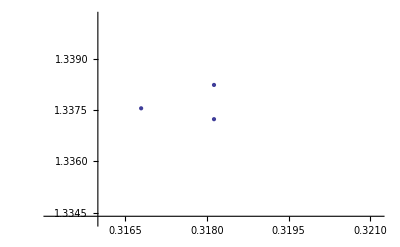

```mathematica
r0=0.001Exp[0.5π I];
ListPlot[ToPlane[{ExpFixPoint,
ExpFixPoint+r0 ,Exp[ExpFixPoint+r0]
(*ExpFixPoint+0.25r0 ,Exp[ExpFixPoint+0.25r0],*)
(*ExpFixPoint+0.5r0 ,Exp[ExpFixPoint+0.5r0],*)
(*ExpFixPoint+0.5r0 ,Exp[ExpFixPoint+0.5r0],*)
(*ExpFixPoint+0.75r0 ,Exp[ExpFixPoint+0.75r0]*)
}],PlotRange->{
{Re[ExpFixPoint]-3Abs[r0],Re[ExpFixPoint]+3Abs[r0]},
{Im[ExpFixPoint]-3Abs[r0],Im[ExpFixPoint]+3Abs[r0]}
}]
```

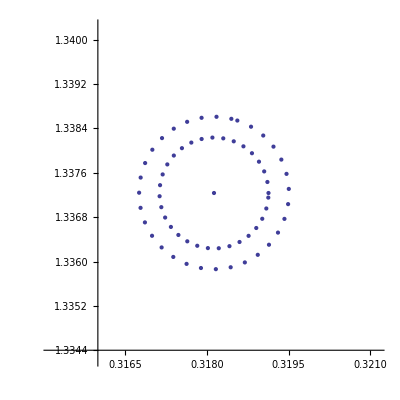

```mathematica
r0=0.001;
ListPlot[ToPlane[
Flatten[{ExpFixPoint, 
Table[{ExpFixPoint+(r0 Exp[ϕ I]),Exp[ExpFixPoint+(r0 Exp[ϕ I])]},
{ϕ,0,2π,0.2}]
}]],
PlotRange->{
{Re[ExpFixPoint]-3Abs[r0],Re[ExpFixPoint]+3Abs[r0]},
{Im[ExpFixPoint]-3Abs[r0],Im[ExpFixPoint]+3Abs[r0]}
},
AspectRatio->1]
```

```mathematica
{ExpFixPoint+r0,Exp[ExpFixPoint+r0]}
```

{0.319132+1.33724 ⅈ,0.31845+1.33857 ⅈ}

```mathematica
r0=0.0000001;
Table[
Module[{res=Exp[ExpFixPoint+(r0 Exp[ϕ I])]},
{ϕ,
Mod[Arg[res-ExpFixPoint]-ϕ,π],
Abs[res-ExpFixPoint]/r0
}
],{ϕ,0,2π,0.2}]
```

{{0.,1.33724,1.37456},{0.2,1.33724,1.37456},{0.4,1.33724,1.37456},{0.6,1.33724,1.37456},{0.8,1.33724,1.37456},{1.,1.33724,1.37456},{1.2,1.33724,1.37456},{1.4,1.33724,1.37456},{1.6,1.33724,1.37456},{1.8,1.33724,1.37456},{2.,1.33724,1.37456},{2.2,1.33724,1.37456},{2.4,1.33724,1.37456},{2.6,1.33724,1.37456},{2.8,1.33724,1.37456},{3.,1.33724,1.37456},{3.2,1.33724,1.37456},{3.4,1.33724,1.37456},{3.6,1.33724,1.37456},{3.8,1.33724,1.37456},{4.,1.33724,1.37456},{4.2,1.33724,1.37456},{4.4,1.33724,1.37456},{4.6,1.33724,1.37456},{4.8,1.33724,1.37456},{5.,1.33724,1.37456},{5.2,1.33724,1.37456},{5.4,1.33724,1.37456},{5.6,1.33724,1.37456},{5.8,1.33724,1.37456},{6.,1.33724,1.37456},{6.2,1.33724,1.37456}}

```mathematica
rfac=1.374557077535672; deltaphi=1.3372357019145538;
ExpSpiral[r0_,phi_,t_]:=ExpFixPoint+
((1-t)r0+t(rfac r0))Exp[I((1-t)phi+t (phi+deltaphi))];
```

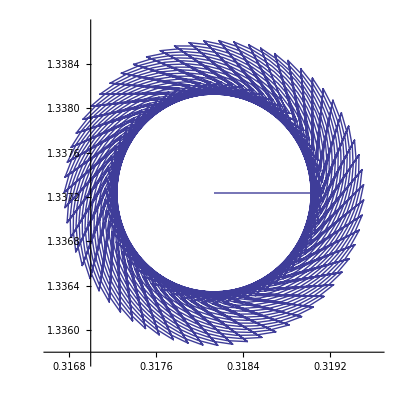

```mathematica
r0=0.001;
ListPlot[ToPlane[
Flatten[{ExpFixPoint, 
Table[{
ExpFixPoint+(r0 Exp[ϕ I]),
Exp[ExpFixPoint+(r0 Exp[ϕ I])],
Table[ExpSpiral[r0,ϕ,t],{t,0,1,0.1}]
},{ϕ,0,2π,0.1}]
}]],
PlotRange->{
{Re[ExpFixPoint]-1.5Abs[r0],Re[ExpFixPoint]+1.5Abs[r0]},
{Im[ExpFixPoint]-1.5Abs[r0],Im[ExpFixPoint]+1.5Abs[r0]}
},
AspectRatio->1,Joined->True]
```

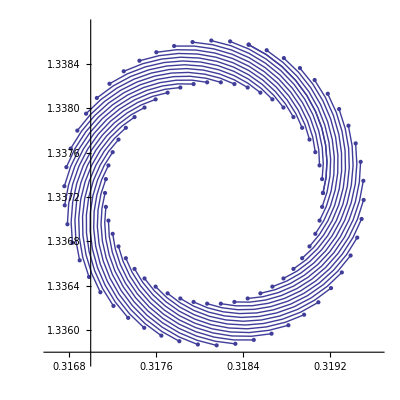

```mathematica
Show[
Table[{
ListPlot[ToPlane[
Table[ExpSpiral[r0,ϕ,t],{t,0,1,0.1}]
],
PlotRange->{
{Re[ExpFixPoint]-1.5Abs[r0],Re[ExpFixPoint]+1.5Abs[r0]},
{Im[ExpFixPoint]-1.5Abs[r0],Im[ExpFixPoint]+1.5Abs[r0]}
},
AspectRatio->1,Joined->True],
ListPlot[ToPlane[{
ExpFixPoint+(r0 Exp[ϕ I]),
Exp[ExpFixPoint+(r0 Exp[ϕ I])]
}]]
},{ϕ,0,2π,2π/50}]
]
```

```mathematica
ExpSpiralInv[r0_,s_]:=
Module[
{t=(Abs[s-ExpFixPoint]-r0)/((rfac-1)r0)},
{Arg[s-ExpFixPoint]-t deltaphi,t}];
```

```mathematica
ExpSpiralInv[r0,ExpSpiral[r0,-0.5,0.5]]
```

{-0.5,0.5}

```mathematica
ExpSpiralVal[phi_,t_]:=t+Exp[I phi];
ExpSpiralVal[s_]:=Module[{phi,t},
{phi,t}=ExpSpiralInv[r0,s];
ExpSpiralVal[phi,t]];
```

```mathematica
ExpSpiralVal[ExpSpiral[r0,0.2,1]]
```

1.98007+0.198669 ⅈ

```mathematica
ExpSpiralInv[r0,Log[Log[Log[0.1]]]]
```

{-3070.54,2296.16}

```mathematica
PhiVal[p_]:=Module[{dist=Abs[p-ExpFixPoint]},
Which[
dist<r0,Indeterminate,
r0≤dist<r0 rfac,ExpSpiralVal[p],
r0 rfac ≤dist,1+ExpSpiralVal[Log[p]]
]
];
```

```mathematica
PhiVal[ExpFixPoint+0.004]
```

5.8037-0.956082 ⅈ

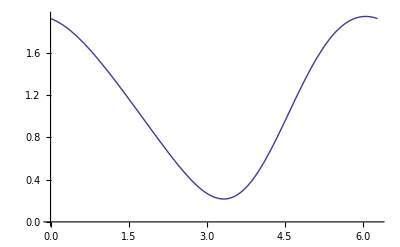

```mathematica
Plot[Re[PhiVal[ExpSpiral[r0,phi,1.1]]],{phi,0,2π}]
```

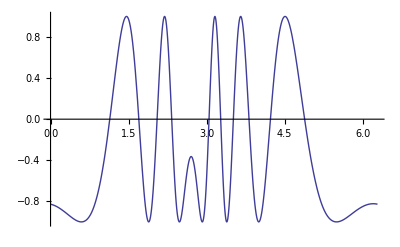

```mathematica
Plot[Im[PhiVal[ExpSpiral[r0,phi,20.1]]],{phi,0,2π}]
```

```mathematica
PlotComplex[f_,rng_]:=Module[{rmin,imin,rmax,imax},
{rmin,imin,rmax,imax}=rng/.{Complex[rmin_,imin_],Complex[rmax_,imax_]}->{rmin,imin,rmax,imax};
GraphicsRow[{
DensityPlot[Abs[f[x+y I]],{x,rmin,rmax},{y,imin,imax},PlotLabel->"Abs",ColorFunction->"TemperatureMap"],
DensityPlot[Arg[f[x+y I]],{x,rmin,rmax},{y,imin,imax},PlotLabel->"Arg",ColorFunction->"TemperatureMap"]
}]
];

PlotComplexReIm[f_,rng_]:=Module[{rmin,imin,rmax,imax},
{rmin,imin,rmax,imax}=rng/.{Complex[rmin_,imin_],Complex[rmax_,imax_]}->{rmin,imin,rmax,imax};
GraphicsRow[{
DensityPlot[Re[f[x+y I]],{x,rmin,rmax},{y,imin,imax},PlotLabel->"Re",ColorFunction->"TemperatureMap"],
DensityPlot[Im[f[x+y I]],{x,rmin,rmax},{y,imin,imax},PlotLabel->"Im",ColorFunction->"TemperatureMap",PlotPoints->100]
}]
];
```

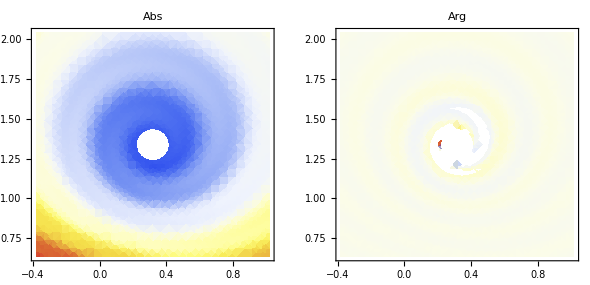

```mathematica
r0=0.1;
idir=1+I;
PlotComplex[PhiVal,{ExpFixPoint-0.7idir,ExpFixPoint+0.7idir}]
```

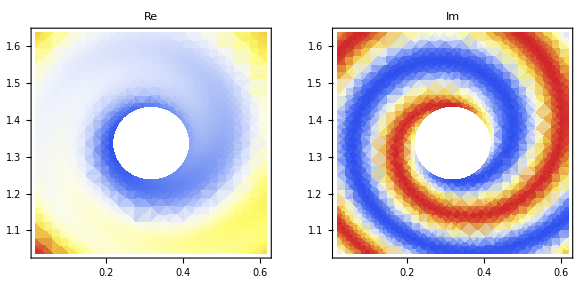

```mathematica
PlotComplexReIm[PhiVal,{ExpFixPoint-0.3idir,ExpFixPoint+0.3idir}]
```

```mathematica
r0=0.05;
PlotComplexReIm[PhiVal,{-1-0.1I,3+3I}]
```

-Graphics-

```mathematica
PlotComplexReIm[PhiVal,{-0.2-0.2I,0.2+0.2I}]
```

-Graphics-

```mathematica
ExpFixPoint
```

0.318132+1.33724 ⅈ